# 🎱 Quantum Walks in Billiards: A Beginner’s Guide

Welcome! In this notebook, we will simulate a Discrete-Time Quantum Walk (DTQW) inside a 2D billiard geometry. If you are familiar with a particle in a box from quantum mechanics, imagine that particle moving on a discrete grid, carrying an internal “coin” (spin) that tells it which way to turn.

We will use the QuantumWalks library to handle the complex linear algebra efficiently.

## 1. Setup and Initialization

First, we need to load our library. > Note: Make sure the QuantumWalks folder is in a location Mathematica can see (like FileNameJoin[{$UserBaseDirectory, “Applications”}]) or allows the kernel to find it.

```mathematica
(*Load the QutumWalks package*)
<<QuantumWalks`
<<QMB`
```

## 2. Defining the Geometry

First you must decide one of these geometries:

Rectangle (integrable)

Ellipse (integrable)

Bunimovich (chaotic), you may choose to work in the dessymetrized or full stadium

Sinai (chaotic), you may choose to work in the dessymetrized or full billiard

Cardiod (chaotic), only full billiard available for now

Let us choose the Bunimovich dessymetrized billiard. First we must generate the basis for the position grid space:

```mathematica
?GenerateSinaiBasis
```

Total number of grid points (N): 5111

Total Hilbert Space Dimension (2N): 10222

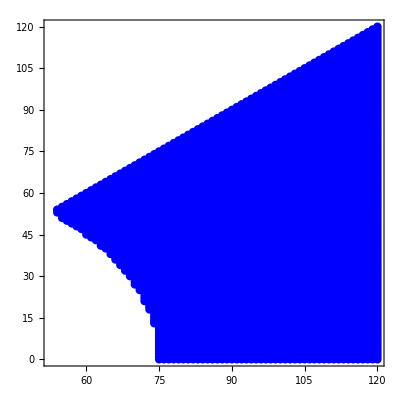

```mathematica
(*Define geometry parameters*)
xc=50; (*Length of the straight part*)
nu=50;  (*Radius (width)*)

(*Generate the grid data*)
billiardData=GenerateStadiumBasis[xc,nu];(*For the full stadium use GenerateFullStadiumBasis*)
billiardData=GenerateCardioidBasis[17];
billiardData=GenerateSinaiBasis[120,75];

(*Let's see what we built*)
Print["Total number of grid points (N): ",billiardData["Dimension"]];
Print["Total Hilbert Space Dimension (2N): ",2*billiardData["Dimension"]];

(*Visualize the grid*)
ListPlot[billiardData["Coords"],PlotStyle->{PointSize[0.015],Blue},AspectRatio->1,Frame->True]
```

## 3. Building the Operators

For a 2D walk, we need:

The Coin (C): Rotates the internal spin state.

The Shift operators (S_x, S_y): Move the particle Left/Right and Up/Down based on its spin.

The library function BuildShiftOperators does the heavy lifting of handling boundary conditions (bouncing off walls) using Sparse Arrays to save memory.

```mathematica
(*1. Construct Shift Operators*)
(*Returns a list {Wm,Wn}*)
{Sx,Sy}=BuildShiftOperators[billiardData];

(*2. Construct the Coin Operator*)
(*We use a standard Hadamard-like coin with angle Pi/4*)
dim=billiardData["Dimension"];
Coin1=Coin[Pi/4.,dim];
Coin2=Coin[Pi/4.,dim];

(*Check if the operators are Unitary (Preserve probability)*)
(*This is a good physics check!*)
unitaryCheck=UnitaryMatrixQ[Sy]&&UnitaryMatrixQ[Sx]&&UnitaryMatrixQ[Coin1]&&UnitaryMatrixQ[Coin2];
Print["Are our operators valid unitary matrices? ",unitaryCheck];
```

Are our operators valid unitary matrices? True

## 4. The Evolution Operator

A single time step (U) in a 2D Split-Step Quantum Walk is often defined as: ψ_(t+1)=S_x C_2 S_y C_1

This means: Flip the coin, then Move vertrically, flip once again the coin, then Move Vertically.

```mathematica
(*Define the single step evolution operator*)
U=Sx.Coin2.Sy.Coin1
```

SparseArray[…]

## 5. Preparing the Initial State

We will start with a Gaussian Wavepacket localized in the center of the stadium . The state is a vector of size $2N$ (Position $\otimes$ Spin) . We must normalize it so total probability $\sum | \psi | ^2 = 1 $ .

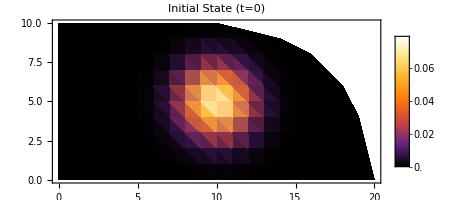

```mathematica
(*Helper to find the index of the center point*)
coords=billiardData["Coords"];
centerPoint={Floor[(xc+nu)/2],Floor[nu/2]}; (*Approximate center*)

(*Create a Gaussian envelope function*)
GaussianPacket[pos_]:=Exp[-Norm[pos-centerPoint]^2/(2.0*2.^2)];

(*Build the spatial vector*)
spatialAmplitudes=GaussianPacket/@coords;

(*Combine with an initial Spin UP state:{1,0}*)
(*We KroneckerProduct the spatial part with the spin part*)
psi0=Flatten[KroneckerProduct[spatialAmplitudes,{1,0} (*Spin Up*)]];

(*NORMALIZE the state*)
psi0=Normalize[psi0];

(*Visualize initial probability*)
ListDensityPlot[
Flatten/@Transpose[{coords,Partition[Abs[psi0]^2,2][[All,1]]+Partition[Abs[psi0]^2,2][[All,2]]}],
ColorFunction->"SunsetColors",PlotLabel->"Initial State (t=0)",PlotRange->All,AspectRatio->Automatic,PlotLegends->Automatic]
```

## 6. Time Evolution (The Walk)

Now we let the particle walk! We calculate the state for 30 time steps.We use NestList which is a functional way to do: $x_0, f(x_0), f(f(x_0))...$

```mathematica
(*Number of steps*)
tMax=30;

(*Evolve!*)
(*This applies EvolutionStep repeatedly to psi0*)
trajectory=NestList[U.#&,psi0,tMax];

Print["Simulation complete. Generated ",Length[trajectory]," states."];
```

Simulation complete. Generated 31 states.

## 7. Visualization and Analysis

Let’s look at the probability distribution $|\psi(t)|^2$ at the final step. In Quantum Walks, unlike classical random walks, you will see interference patterns and ballistic spreading (moving faster than diffusion).

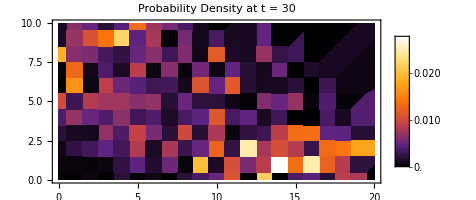

```mathematica
(*Function to convert state vector to plot-able data*)
StateToPlotData[stateVector_,coordinates_]:=Module[
{probs},
(*1. Calculate|amplitude|^2*)
probs=Abs[stateVector]^2;
(*2. Sum Up and Down spin components for each site*)
(*The vector is {Site1_Up,Site1_Down,Site2_Up,Site2_Down...}*)
(*We partition by 2 and sum the sublists*)
probs=Total/@Partition[probs,2];
(*3. Combine with coordinates*)
MapThread[Append,{coordinates,probs}]
];

(*Plot the final state*)
finalPlotData=StateToPlotData[Last[trajectory],coords];

ListDensityPlot[finalPlotData,
ColorFunction->"SunsetColors",PlotLabel->Row[{"Probability Density at t = ",tMax}],PlotRange->All,AspectRatio->Automatic,PlotLegends->Automatic,InterpolationOrder->0]
```

```mathematica
ListAnimate[ListDensityPlot[StateToPlotData[#,coords],
ColorFunction->"SunsetColors",PlotLabel->Row[{"Probability Density at t = ",tMax}],PlotRange->All,AspectRatio->Automatic,PlotLegends->Automatic,InterpolationOrder->0]&/@trajectory]
```